## data

```mathematica
MuC310pdata={{0.016701608074071395,0.07754069069407973,0.06283447273592388,0.02209102383372554,0.01341948479149841,0.02583899946393066,0.014938494793983983,0.03570199903528294,0.14292293275616405,0.0010003653939634435,0.09266403324715593,0.09297518505365107},{0.014159539029454585,0.030133525435035485,0.06186589070813571,0.01760050922418138,0.011346091771891102,0.017494244267067298,0.012968440432359531,0.01825529090810447,0.04892614401224156,0.0010003653939634435,0.07553108052162515,0.0755300936051257}};

MuC1010pdata={{0.003944915385853956,0.013899938868691251,0.018266400456266416,0.0055740847931749805,0.003054443799633908,0.006785552299612656,0.003139285945160854,0.008993374351033215,0.02880000608799413,0.001000028227486939,0.020370088792460675,0.02038761161416352},{0.0037798032831557493,0.012498062502802162,0.018213340358617207,0.005353783474522144,0.0029055821048615395,0.00633508725925277,0.003071945747221672,0.007865847185028432,0.024986246601573465,0.0009997686517950206,0.019210725079119167,0.019196972997927105}};

cepc36010pdata={{0.004356921169265702,1.2,0.010918877258039698,0.006149129152021536,0.004254098665208407,0.005109585301674397,0.0009591395897476812,0.015016994693702886,0.03157401745364771,0.0014000045624755757,0.0060737897225673415,0.01067289187544299},{0.004124283873140328,0.030605518641826743,0.010825331571333903,0.005768039279964398,0.004008229870257032,0.004827346072517949,0.000956676173859419,0.010515499220697031,0.02668924107498834,0.0013992951632438896,0.006058911001620974,0.010211965505983423}};

MuC10cepc360LHC10pdata={{0.0032739412747150964,0.02803043988457233,0.010341206276879823,0.00499274913664491,0.0027235353282191784,0.0040535588719349345,0.0009501219773855325,0.009806186746506195,0.026129634927008927,0.0008135968498495776,0.005908857327187712,0.008653828146112263},{0.002049076358055006,0.012266365913420674,0.008847348628314718,0.003375867718212157,0.0012590703795964584,0.0029269045583653367,0.0008847726033293919,0.006454670390982625,0.01945526916308487,0.0008135964975715133,0.005511422944922295,0.006518114345419188},{0.0031384007638786023,0.006359576889362369,0.009625035986431784,0.004915602326906001,0.002600936202427696,0.003923040323624988,0.0009325991952896595,0.007904584012583368,0.0037158637018259626,0.0008135968596677538,0.005697497560782565,0},{0.0019904727584105462,0.0054812874442448645,0.008376016854712388,0.003346431990913363,0.0012141505592548417,0.002874112873882729,0.0008650542314582647,0.005768333595521171,0.003613477294902104,0.000813596569228587,0.005292817793439364,0},{0,0,0,0,0,0,0,0,0,0,0,0}};
```

# Plotting

### only MuC 10TeV, only CEPC 240GeV, only CEPC 240+360GeV, only MuC 10TeV + CEPC 240+360 GeV +HL-LHC

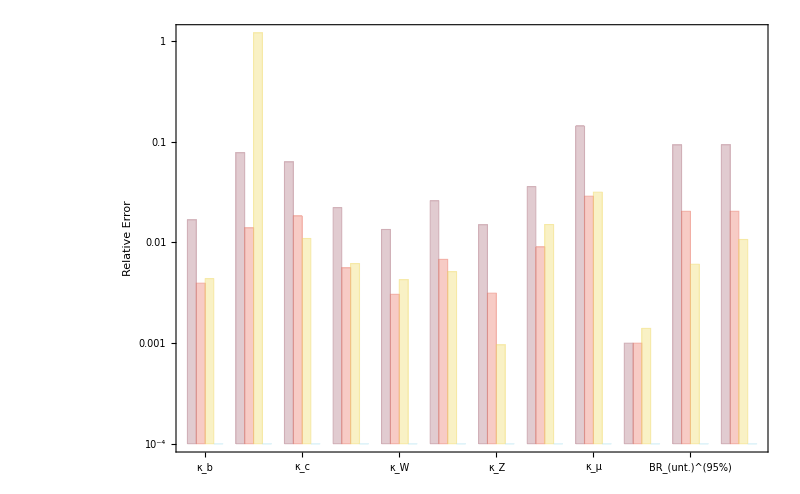

```mathematica
data1={MuC310pdata[[1]],MuC1010pdata[[1]],cepc36010pdata[[1]],MuC10cepc360LHC10pdata[[5]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",18],Style["\!\(\*SubsuperscriptBox[\(BR\), \(unt.\), \(95%\)]\)",18],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (11-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]}},BaseStyle->28,PlotRange->{{1,66},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC10TeV+HLLHC, CEPC240GeV+HLLHC, CEPC240+360GeV+HLLHC, MuC10TeV+CEPC240+360GeV+HLLHC+MuC125GeV

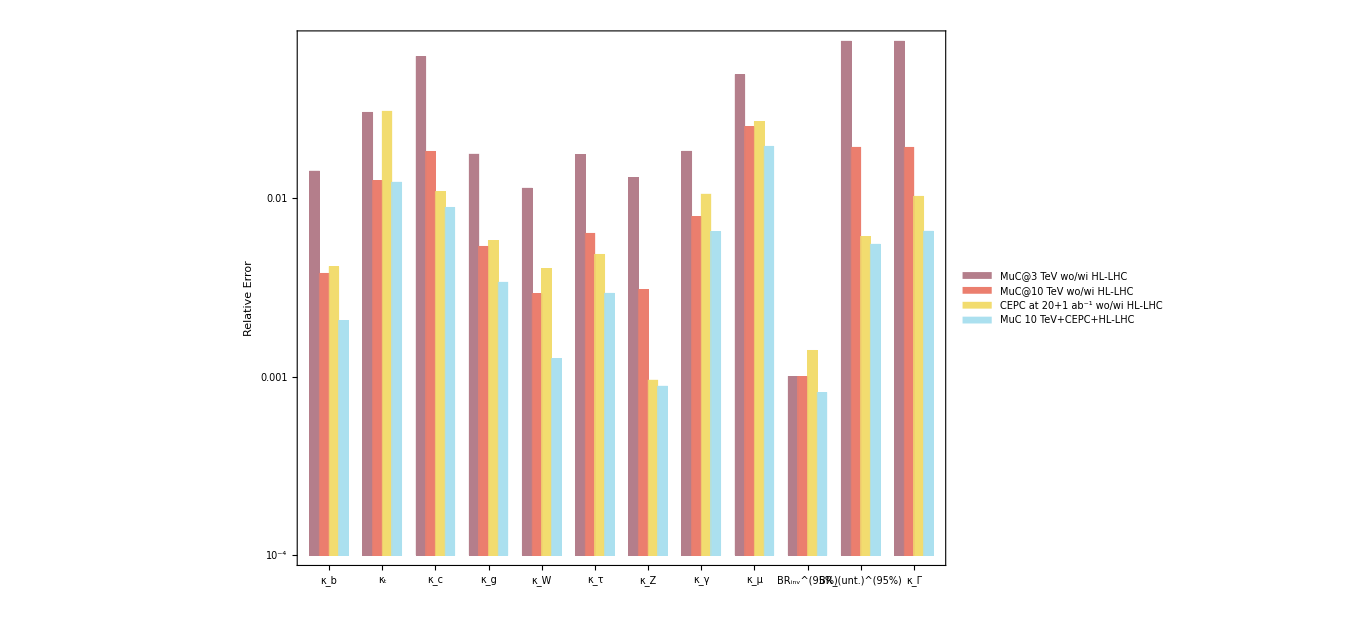

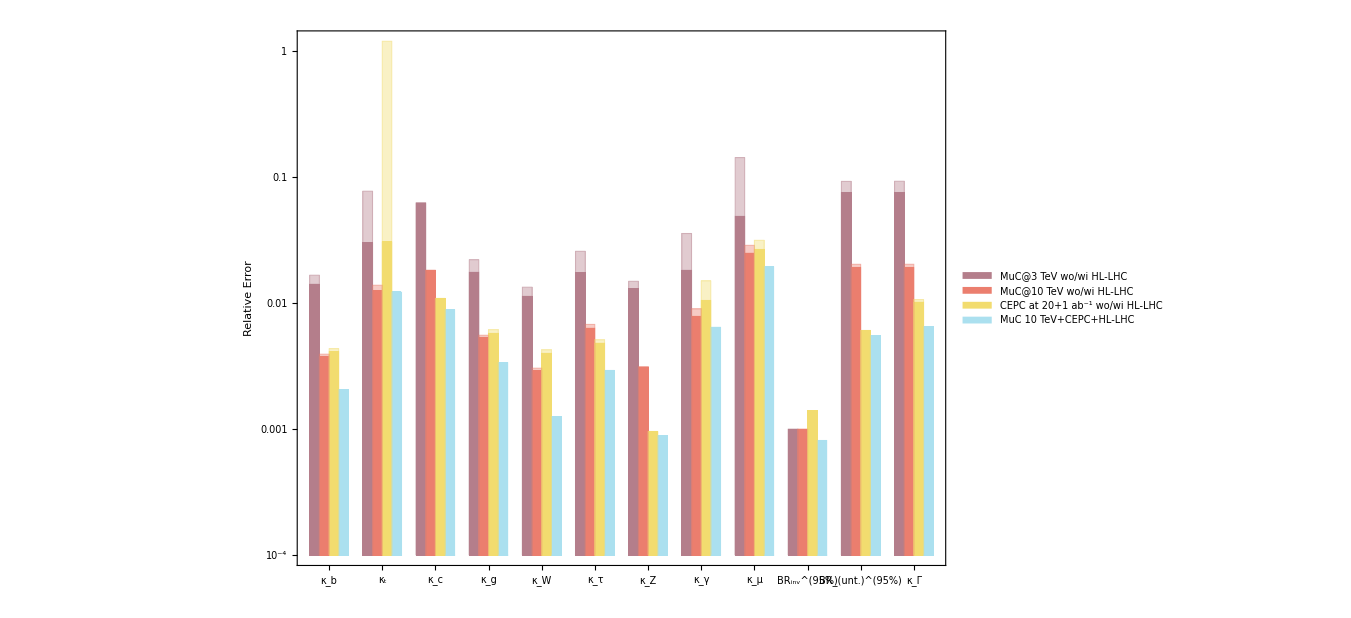

```mathematica
data2={MuC310pdata[[2]],MuC1010pdata[[2]],cepc36010pdata[[2]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",20],Style["\!\(\*SubsuperscriptBox[\(BR\), \(unt.\), \(95%\)]\)",20],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (11-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]},BaseStyle->28,PlotRange->{{1,66},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->1000,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi HL-LHC",18],Style["MuC@10 TeV wo/wi HL-LHC",18],Style["CEPC at 20+1 ab^-1 wo/wi HL-LHC",18],Style["MuC 10 TeV+CEPC+HL-LHC",18]},Scaled[{{0.22,0.64},{0,0}}]]]
Show[p10fit2,p10fit1]
```

### only MuC 3TeV, only MuC 10TeV, only CEPC 240GeV

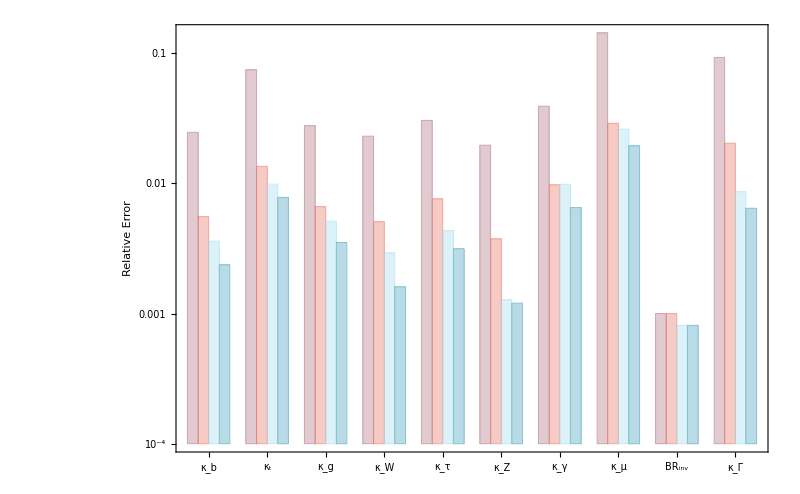

```mathematica
data1={MuC3MuC12510pdata[[1]],MuC10MuC12510pdata[[1]],MuC10cepc360LHC10pdata[[1]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]}},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,0.5}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC3TeV+125GeV, MuC10TeV+125GeV, CEPC240GeV+360GeV

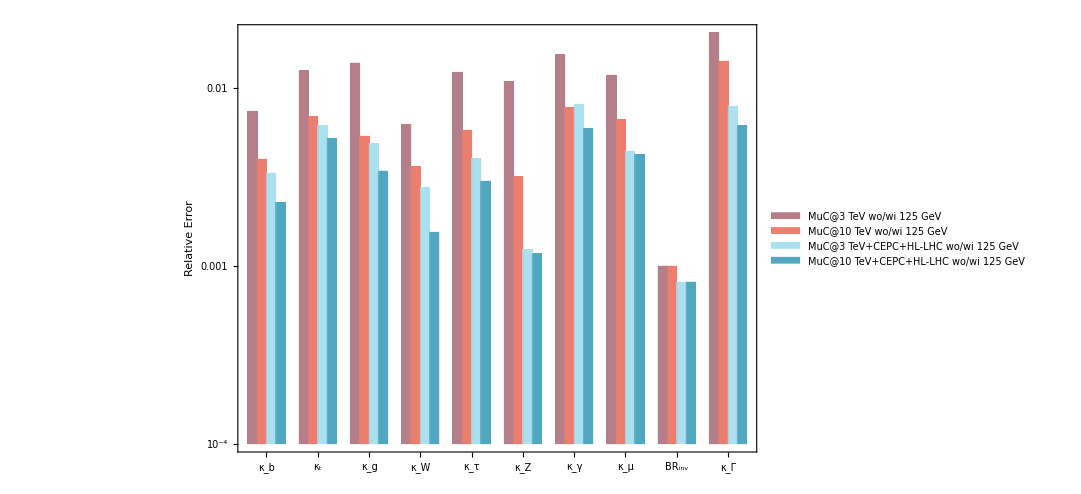

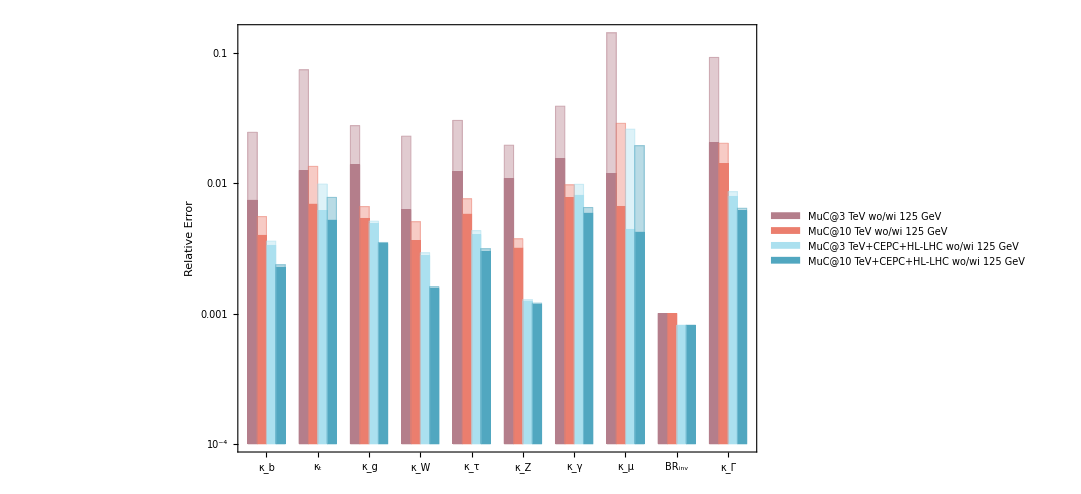

```mathematica
data2={MuC3MuC12510pdata[[2]],MuC10MuC12510pdata[[2]],MuC10cepc360LHC10pdata[[3]],MuC10cepc360LHC10pdata[[4]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubscriptBox[\(BR\), \(inv\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi 125 GeV",18],Style["MuC@10 TeV wo/wi 125 GeV",18],Style["MuC@3 TeV+CEPC+HL-LHC wo/wi 125 GeV",18],Style["MuC@10 TeV+CEPC+HL-LHC wo/wi 125 GeV",18]},Scaled[{{0.14,0.55},{0,0}}]]]
Show[p10fit2,p10fit1]
```